Нач данные

```mathematica
B0=1015 10^2;
R=287.4;
T0=27+273;
roj=1000;
g=9.86;
beta=20Degree;
```

```mathematica
gr[x_]:=Grid[{Range[Length[x]],x}ᵀ,Frame->All]
grT[x_]:=Grid[Prepend[x,Range[Length[x[[1]]]]]ᵀ,Frame->All]
```

Эксп данные

```mathematica
Hoi={350,353,360,355,352,355,355,360,356};
Hki={{223,201,219,225,260,312,343,347,349},{223,202,225,236,275,319,345,349,351},{223,204,228,245,285,329,349,350,352},{223,206,226,256,297,335,351,352,353}};
```

```mathematica
ro0=B0/(R T0)
```

1.17722

```mathematica
dHki=Table[Hoi-Hki[[i]],{i,Length[Hki]}];
grT[dHki]
```

1 | 127 | 127 | 127 | 127
2 | 152 | 151 | 149 | 147
3 | 141 | 135 | 132 | 134
4 | 130 | 119 | 110 | 99
5 | 92 | 77 | 67 | 55
6 | 43 | 36 | 26 | 20
7 | 12 | 10 | 6 | 4
8 | 13 | 11 | 10 | 8
9 | 7 | 5 | 4 | 3

```mathematica
Vki1=√(2 (roj g dHki Sin[beta])/(1000 ro0));
grT[Vki1]
```

1 | 26.9744 | 26.9744 | 26.9744 | 26.9744
2 | 29.5102 | 29.413 | 29.2175 | 29.0208
3 | 28.4223 | 27.811 | 27.5003 | 27.7078
4 | 27.2912 | 26.111 | 25.1042 | 23.8159
5 | 22.9585 | 21.0037 | 19.5924 | 17.7514
6 | 15.6958 | 14.3616 | 12.205 | 10.7045
7 | 8.29165 | 7.56921 | 5.86308 | 4.78719
8 | 8.63022 | 7.93865 | 7.56921 | 6.7701
9 | 6.33285 | 5.35224 | 4.78719 | 4.14582

```mathematica
Vki=Flatten[Vki1ᵀ];
Vki[[1]]=29.5;
Vki[[2]]=29.4;
Vki[[3]]=29.02;
Vki[[-8;;-1]]=Vki[[-8;;-1]]-Vki[[-1]]
Vki
Length[Vki]
```

{4.4844,3.79283,3.42338,2.62428,2.18703,1.20641,0.641361,0.}

{29.5,29.4,29.02,26.9744,29.5102,29.413,29.2175,29.0208,28.4223,27.811,27.5003,27.7078,27.2912,26.111,25.1042,23.8159,22.9585,21.0037,19.5924,17.7514,15.6958,14.3616,12.205,10.7045,8.29165,7.56921,5.86308,4.78719,4.4844,3.79283,3.42338,2.62428,2.18703,1.20641,0.641361,0.}

36

```mathematica
Y=Range[18,18+35]*5
Length[Y]
```

{90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265}

36

Задать Y1 и Y2!

```mathematica
Y1=110;
Y2=265;
```

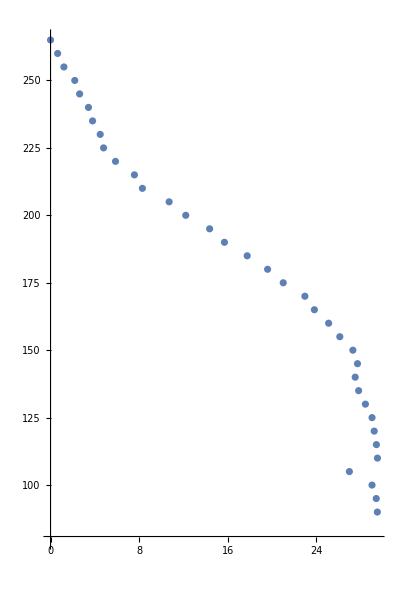

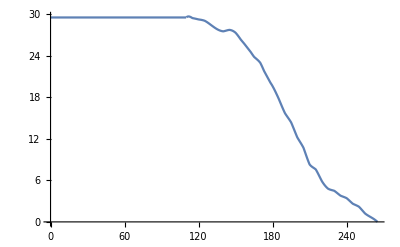

```mathematica
V[y_]:=Piecewise[{{Vki[[1]],y≤ Y1},{Interpolation[{Y,Vki}ᵀ,y],y>110}}]
ListPlot[{Vki,Y}ᵀ,AspectRatio->1.5,PlotRange->{80,265}]
Plot[V[y],{y,0,Y2}]
```

```mathematica
X0=150/Tan[12.5Degree]
```

676.606

```mathematica
bp=3.16 150;
x2=bp/Tan[12.5Degree];
xnach=150/Tan[6.5Degree];
X0=(x2-1.5xnach)
```

163.276

V/Vm=(1-(y/b)^(3/2))^2

Задать Vm и b!

```mathematica
Vm=29.5;
b=0.27  (450-X0)
```

77.4154

```mathematica
Vt[y_]:=Vm*(1-((y-115)/(285-115))^(3/2))^2
```

```mathematica
Grid[{Range[1,Length[Range[110,265,(265-110)/9]]],N@Range[110,265,(265-110)/9],Vt[Range[110,265,(265-110)/9]]}ᵀ,Frame->All]
```

1 | 110. | 29.5
2 | 127.222 | 27.7797
3 | 144.444 | 24.7679
4 | 161.667 | 21.1245
5 | 178.889 | 17.1846
6 | 196.111 | 13.2075
7 | 213.333 | 9.41838
8 | 230.556 | 6.02389
9 | 247.778 | 3.219
10 | 265. | 1.19091

```mathematica
29.4 (0.3 ro0)/(1.7 10^-5)
```

610770.

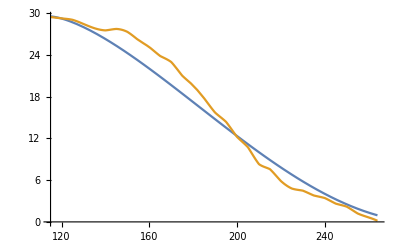

```mathematica
Plot[{Vt[y],V[y]},{y,115,264}]
```

10. Определение расхода интегрированием

```mathematica
Q0=Pi 150^2 29.4/10^6
```

2.07816

```mathematica
Qe=NIntegrate[2Pi y V[y],{y,0,265}]/10^6
```

3.58877

```mathematica
Q=NIntegrate[2Pi y Vt[y],{y,115,265}]/10^6
```

2.30944

11. Расход через начальное сечение струи

Задать V0!

```mathematica
V0=29.4;
```

```mathematica
Q0=V0 b/2
```

(b V0)/2

12. Теоретическое значение расхода по формуле 4 или 4’

Задать X и b0!

```mathematica
X=450;
b0=150;
```

Подставить номер формулы!

```mathematica
Qt=Q0{ 0.375 √(X/b0),1+0.036 X/b0}[[2]]
```

2.30261

13. Сравнить:

```mathematica
dQ=Abs[Qe-Qt]
delQ=dQ/Qt 100
```

1.28616

55.8568

14.

```mathematica
ki=Vki^2 ro0;
kif[y_]:=Interpolation[{Range[0,Length[ki]-1]*5,ki}ᵀ,y]
Grid[{Range[1,Length[ki]],Range[0,Length[ki]-1]*5,ki}ᵀ,Frame->All]
```

1 | 0 | 1024.48
2 | 5 | 1017.54
3 | 10 | 991.409
4 | 15 | 856.569
5 | 20 | 1025.18
6 | 25 | 1018.44
7 | 30 | 1004.95
8 | 35 | 991.462
9 | 40 | 950.994
10 | 45 | 910.526
11 | 50 | 890.292
12 | 55 | 903.781
13 | 60 | 876.803
14 | 65 | 802.612
15 | 70 | 741.91
16 | 75 | 667.719
17 | 80 | 620.507
18 | 85 | 519.337
19 | 90 | 451.891
20 | 95 | 370.955
21 | 100 | 290.019
22 | 105 | 242.807
23 | 110 | 175.361
24 | 115 | 134.893
25 | 120 | 80.9356
26 | 125 | 67.4464
27 | 130 | 40.4678
28 | 135 | 26.9785
29 | 140 | 23.6737
30 | 145 | 16.9349
31 | 150 | 13.7965
32 | 155 | 8.10733
33 | 160 | 5.63075
34 | 165 | 1.71336
35 | 170 | 0.484243
36 | 175 | 0.

15.

```mathematica
Plot[kif[y],{y,0,Y1}]
```

16. Определить количество движения ж-ти в данном сечении:

```mathematica
Kk=NIntegrate[kif[y],{y,0,Y1}];
```

17. Определить количество движения ж-ти в начальном сечении:

```mathematica
K0=ro0 V0^2 b/2
```

```mathematica
(0.0017397355601948504 b B0 V0^2)/T0
```

45.5675 V0^2

18. Сравнить:

```mathematica
dK=Abs[K0-Kk]
delL=dK/K0 100
```

Abs[K0-Kk]

(100 Abs[K0-Kk])/K0

20, 21

```mathematica
Va={0.45Vm,(1+0.036 X/b0)/(1+0.158 X/b0)V0}[[;;]]
Vq={0.7Vm,1/(1+0.036 X/b0)V0}[[;;]]
```

{0.45 Vm,(V0 (1+(0.036 X)/b0))/(1+(0.158 X)/b0)}

{0.7 Vm,V0/(1+(0.036 X)/b0)}

23.

```mathematica
ei=ro0 Vki^3;
eif[y_]:=Interpolation[{Range[0,Length[ei]-1]*5,ei}ᵀ,y]
gr[ei]
```

1 | (8125.87 B0 ((roj T0)/B0)^(3/2))/T0
2 | (7131.6 B0 ((roj T0)/B0)^(3/2))/T0
3 | 0.
4 | (33739.7 B0 ((roj T0)/B0)^(3/2))/T0
5 | (35385.3 B0 ((roj T0)/B0)^(3/2))/T0
6 | (35385.3 B0 ((roj T0)/B0)^(3/2))/T0
7 | (37056.9 B0 (-(roj T0)/B0)^(3/2))/T0
8 | (1563.82 B0 ((roj T0)/B0)^(3/2))/T0
9 | (8125.87 B0 ((roj T0)/B0)^(3/2))/T0

24.

```mathematica
Plot[eif[y],{y,0,Y1}]
```

25.

```mathematica
Ee=NIntegrate[eif[y],{y,0,Y1}]
```

26.

```mathematica
E0=E0;
Et=E0{3.01 X/b0 1/(X/b0-X0/b0)^(3/2),1-0.019 X/b0}[[;;]]
```

{(3.01 E0 X)/(b0 (X/b0-X0/b0)^(3/2)),E0 (1-(0.019 X)/b0)}

27.

```mathematica
dE=Abs[Ee-Et]
delE=dE/Ee*100
```